```mathematica
Lecture 7:Graphics
```

## Plotting lists and matrices

### Exercise Subsection

The Conway recursive sequence is defined by the following cell:

```mathematica
Clear[a]
a[n_]:=a[n]=If[n<=2,1,a[a[n-1]]+a[n-a[n-1]]]
```

Use ListPlot to plot the list of terms of the form a[n]/n where n ranges from 1 to 10000.

### Exercise Subsection

Illustrate that the number of primes numbers <= n grows approximately at the same rate as the function n/Log[n] by plotting the list of terms of the form PrimePi[n]/(n/Log[n]) for n = 2,...,10^5 and observing that the terms approach a limiting value.

### Exercise Subsection

Use ListPlot to plot these {x,y} coordinates in the plane twice, once with and once without the Joined->True option.

```mathematica
coordinates={{269,400},{298,389},{311,363},{308,325},{297,280},{283,235},{270,194},{262,153},{255,112},{247,69},{236,23},{224,-22},{212,-66},{202,-109},{194,-152},{186,-196},{176,-240},{164,-283},{153,-326},{144,-370},{137,-416},{132,-463},{129,-510},{127,-556},{127,-600},{132,-644},{145,-687},{166,-730},{193,-768},{227,-799},{265,-822},{307,-834},{353,-839},{399,-835},{441,-822},{476,-798},{500,-763},{512,-719},{512,-671},{503,-625},{483,-585},{456,-551},{423,-521},{389,-490},{359,-455},{338,-416},{326,-373},{325,-326},{331,-280},{341,-235},{352,-193},{362,-153},{372,-112},{382,-71},{392,-26},{403,19},{414,64},{425,106},{436,147},{446,189},{455,234},{464,281},{474,325},{489,362},{512,388},{546,402},{590,405},{642,402},{695,397},{743,394},{782,399},{813,416},{836,448},{853,492},{863,540},{864,583},{850,613},{821,626},{779,627},{729,623},{678,620},{629,621},{585,623},{541,625},{496,624},{448,623},{399,621},{351,622},{306,623},{261,624},{215,624},{168,623},{120,622},{72,622},{26,622},{-19,623},{-64,623},{-111,623},{-159,623},{-209,622},{-257,619},{-302,612},{-345,600},{-386,581},{-426,557},{-463,529},{-498,497},{-529,464},{-557,431},{-584,398},{-612,364},{-640,327},{-665,288},{-681,251},{-685,224},{-673,216},{-647,231},{-612,263},{-573,304},{-536,341},{-500,367},{-464,382},{-424,389},{-377,395},{-325,402},{-274,406},{-232,402},{-205,388},{-197,361},{-204,325},{-219,284},{-237,243},{-252,202},{-263,163},{-274,125},{-285,86},{-299,48},{-313,8},{-327,-33},{-340,-73},{-352,-112},{-363,-148},{-375,-183},{-387,-220},{-400,-259},{-415,-300},{-436,-343},{-463,-383},{-497,-420},{-538,-454},{-580,-486},{-622,-519},{-660,-552},{-694,-586},{-723,-622},{-745,-661},{-757,-705},{-756,-750},{-739,-792},{-709,-824},{-668,-840},{-622,-841},{-576,-829},{-534,-809},{-498,-784},{-466,-755},{-439,-723},{-415,-687},{-393,-648},{-373,-609},{-355,-571},{-338,-532},{-322,-491},{-306,-449},{-290,-408},{-276,-368},{-263,-332},{-250,-296},{-237,-257},{-223,-213},{-208,-167},{-192,-122},{-178,-81},{-165,-43},{-153,-6},{-140,33},{-127,75},{-111,119},{-95,161},{-81,201},{-69,241},{-58,283},{-46,325},{-28,361},{-3,387},{31,400},{74,402},{124,400},{176,400},{227,402},{269,400}};
```

```mathematica
G1=ListPlot[coordinates,AspectRatio->1,Joined->True,Axes->False];
G2=ListPlot[coordinates];
Show[G1,G2]
```

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

### Exercise Subsection

Use MatrixPlot to plot the matrix binmat[n] for various inputs n where binmat[n] is the matrix defined by the following cell:

```mathematica
binmat[n_]:=Table[Mod[Binomial[i,j],2],{i,0,n},{j,0,n}]
```

### Exercise Subsection

Use MatrixPlot to plot the 100x100 matrix with i,j entry equal to the greatest common divisor (the GCD) of i and j.

## Plotting in 2D

### Exercise Subsection

Compare the graphs of 1-π/2+(4 Cos[x])/π+(4 Cos[3 x])/(9 π)+(4 Cos[5 x])/(25 π)+(4 Cos[7 x])/(49 π) and 1-Abs[x] by using Plot to plot these functions on the same axes.

### Exercise Subsection

Use ParametricPlot to show plot the curve described by the parametric equations defined in the next cell.

```mathematica
f[t_]:=(E^Cos[t] - 2 Cos[4 t]-Sin[t/12]^5);
x[t_]:=Sin[t] f[t];
y[t_]:=Cos[t]f[t];
```

```mathematica
Show[ListPlot[Table[N@{x[t],y[t]},{t,0,2Pi,Pi/240}],AspectRatio->1],ParametricPlot[{x[t],y[t]},{t,0,2Pi}]]
```

### Exercise Subsection

What does the following cell do when evaluated?

```mathematica
G1=ListPlot[{Cos[#], Sin[2 #]}&/@Range[0,2 Pi,Pi/50],AspectRatio->1];
G2=ParametricPlot[{Cos[t],Sin[2 t]},{t,0,2Pi},PlotStyle->{Red,Thin}];
Show[G1,G2]
```

### Exercise Subsection

Use ContourPlot to graph the (x,y) coordinate pairs that satisfy Abs[3x^2 + x y^2 - 2] == Abs[x^2 - y^2 + 4].

## Plotting in 3D

### Exercise Subsection

Compare the Plot3D and the ContourPlot output for the function x Sin[x^2 + y^2]/(x^2 + y^2), playing with the Contours and PlotPoints options for ContourPlot.

```mathematica
Plot3D[x Sin[x^2 + y^2]/(x^2 + y^2),{x,-Pi,Pi},{y,-Pi,Pi},PlotRange->All,AxesLabel->{"x","y","z"},PlotPoints->50]
```

-Graphics3D-

```mathematica
ContourPlot[x Sin[x^2 + y^2]/(x^2 + y^2),{x,-Pi,Pi},{y,-Pi,Pi},PlotPoints->50]
```

### Exercise Subsection

Show the parametric curve {Cos[t]Sin[t],Cos[2 t],Sin[3t]} in R^3 using ParametricPlot3D.

### Exercise Subsection

Use ContourPlot3D to plot the points in R^3 that satisfy (x^2 + (9/4) y^2 + z^2 - 1)^3 - x^2 z^3 - 9 y^2 z^3/80 equalling 0.  Play with the Options in ContourPlot3D, considering adjusting Boxes, Axes, and PlotPoints.

### Exercise Subsection

The trefoil knot is the curve in R^3 described by the parametric equations

```mathematica
{(2+Cos[3 t])Cos[2t],(2+Cos[3t])Sin[2t],Sin[3 t]}
```

Produce a graphic using Show and two cases of ParametricPlot3D that shows the trefoil knot lies on the torus that is parameterized by the parametric equations

```mathematica
x[u_,v_]:=(2+Cos[3u])Cos[v]
y[u_,v_]:=(2+Cos[3u])Sin[v]
z[u_,v_]:=Sin[3u]
```

where t,u,v can all vary from 0 to 2Pi.

## Graphics objects

### Exercise Subsection

Use Graphics to draw all of these objects in the same image: 
a. a Red Line that connects the points {0,0}, {1,1}, {1,0}, {0,1}, 
b. a Green Circle with center at {.5,.5} and radius .5, 
c. a Purple Arrow that connects the points {0,0}, {0,1}, and 
d. a Orange Point with PointSize .1 at {.5,.5}.

```mathematica
Graphics[{Red,Line[{{0,0}, {1,1}, {1,0}, {0,1}}],
Green,Circle[{.5,.5},.5],
Purple,Arrow[{{0,0},{0,1}}],
PointSize[.1],Point[{.5,.5}]
}]
```

### Exercise Subsection

Use Graphics together with Line to draw the ‘g-raph’ created by the line segments that pass through the {x,y} coordinates in the next cell, similar to a dot-to-dot puzzle:

```mathematica
coordinates={{12,-536},{32,-528},{52,-512},{64,-496},{72,-472},{80,-452},{88,-436},{96,-416},{108,-396},{120,-376},{132,-352},{140,-332},{144,-308},{140,-288},{132,-264},{136,-260},{152,-280},{160,-300},{168,-324},{164,-344},{168,-368},{168,-388},{168,-412},{168,-432},{164,-456},{156,-476},{148,-492},{124,-504},{128,-520},{152,-524},{168,-516},{184,-500},{192,-480},{192,-456},{192,-432},{196,-408},{200,-388},{200,-364},{204,-340},{204,-320},{204,-296},{200,-272},{192,-256},{180,-236},{172,-216},{168,-192},{168,-172},{172,-148},{176,-124},{176,-104},{184,-96},{188,-116},{192,-140},{192,-164},{196,-184},{200,-208},{204,-228},{208,-252},{212,-272},{212,-296},{216,-320},{220,-340},{232,-352},{240,-332},{240,-312},{240,-288},{236,-264},{228,-244},{216,-220},{216,-196},{212,-176},{212,-152},{208,-128},{208,-108},{204,-84},{196,-64},{184,-44},{168,-28},{152,-16},{136,0},{116,8},{96,20},{76,28},{56,36},{36,48},{20,64},{4,80},{-12,96},{-20,116},{-32,136},{-40,156},{-52,176},{-64,192},{-80,208},{-80,232},{-80,252},{-84,276},{-88,296},{-88,320},{-88,340},{-88,364},{-84,384},{-80,408},{-80,432},{-68,452},{-44,456},{-20,456},{-4,468},{-16,484},{-40,492},{-36,508},{-32,528},{-52,528},{-68,516},{-88,524},{-108,536},{-132,540},{-152,540},{-172,548},{-192,560},{-216,564},{-232,544},{-216,524},{-196,516},{-180,504},{-172,484},{-156,464},{-148,444},{-144,424},{-144,400},{-148,380},{-156,356},{-164,332},{-172,312},{-176,288},{-176,264},{-184,244},{-188,220},{-188,196},{-188,176},{-184,152},{-180,128},{-176,108},{-176,84},{-176,60},{-180,40},{-192,16},{-196,-8},{-188,-28},{-172,-52},{-160,-76},{-152,-96},{-148,-120},{-152,-144},{-156,-164},{-156,-188},{-156,-212},{-156,-232},{-156,-256},{-164,-280},{-168,-300},{-172,-324},{-172,-348},{-176,-368},{-176,-392},{-184,-416},{-188,-436},{-192,-456},{-200,-480},{-212,-496},{-228,-508},{-236,-528},{-216,-536},{-196,-524},{-180,-508},{-168,-488},{-160,-468},{-156,-444},{-152,-420},{-148,-400},{-140,-376},{-140,-356},{-136,-332},{-124,-308},{-120,-284},{-112,-280},{-112,-304},{-108,-324},{-104,-348},{-100,-372},{-96,-392},{-96,-416},{-96,-440},{-96,-460},{-100,-484},{-120,-508},{-124,-524},{-96,-528},{-80,-512},{-76,-492},{-64,-468},{-64,-444},{-64,-424},{-68,-400},{-72,-376},{-76,-352},{-76,-332},{-76,-308},{-76,-284},{-76,-264},{-80,-240},{-80,-216},{-84,-196},{-84,-172},{-84,-148},{-64,-148},{-40,-148},{-16,-152},{4,-148},{24,-152},{32,-176},{40,-192},{52,-212},{60,-232},{72,-252},{80,-272},{88,-288},{92,-312},{92,-332},{88,-352},{84,-372},{76,-396},{64,-416},{56,-436},{44,-460},{36,-476},{24,-492},{8,-508},{-12,-520},{-12,-536},{12,-536}};
```

```mathematica
Graphics[{Orange,Line@coordinates,Blue,PointSize->.01,Point@coordinates}]
```

### Exercise Subsection

A turtle (see https://en.wikipedia.org/wiki/Turtle_graphics ) takes a random walk of length n in the the plane.  The turtle begins at {0,0} pointing East and then repeats the following steps n times: 

1. the turtle randomly selects a radian angle between 0 and 2Pi and then rotates that angle (relative to its current position).
2. the turtle takes one step forward. 

Use AnglePath together with Line and Graphics to draw one such random walk of length 10000.  Your graphics image should include the x and y Axes.

```mathematica
Graphics[{Purple,Line@(path=AnglePath@Table[(2Pi)Random[],{i,10000}])}]
ListPlot[path,Joined->True]
```

### Exercise Subsection

Recall from Exercise Set 5 that Thue-Morse sequence is a sequence of lists that begins with the list {0} and then subsequent terms in the sequence are found by replacing each 0 in the previous list with 0, 1 and each 1 with 1, 0.  It can be defined using the function in the next cell:

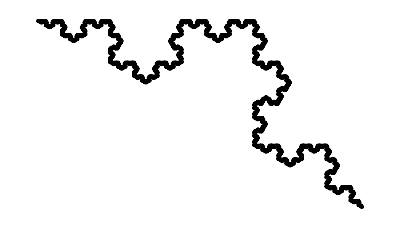

```mathematica
tm[n_]:=Nest[Flatten[#/.{0->{0,1},1->{1,0}}]&,{0},n]
Graphics@Line@AnglePath[tm[15]/.{1->-Pi/3}]
```

## Animations

### Exercise Subsection

Create a list containing the output of the Plot function that shows the graphs of Cos[x]+Sin[x] together with the function Sum[(-1)^(i(i-1)/2) x^i/i!,{i,0,n}] on the interval from -5Pi to 5Pi for values of n=0,1,...,40 Then use ListAnimate to create a ‘movie’ that shows how these polynomials converge to Cos[x]+Sin[x].  To create a good ‘movie’, make sure to set the PlotRange option.

```mathematica
ListAnimate@Table[Plot[{Cos[x]+Sin[x],Sum[(-1)^(i(i-1)/2) x^i/i!,{i,0,n}]},{x,-5Pi,5Pi},PlotRange->{-3,3}],{n,0,40}]
```

### Exercise Subsection

Use ListAnimate to make a ‘movie’ showing how ListPlot[{Cos[#],Sin[#]}&/@Range@n] evolves for values of n ranging from 1 to 400.  Be sure to use the PlotRange and AspectRatio options to improve the animation.

### Exercise Subsection

Use Table to define a 50x50 matrix named mat with i,j entry equal to a random integer between -10 and 10 if i < j and 0 otherwise.  Then use  ListAnimate together with MatrixPlot to illustrate how MatrixPower[mat,n] changes as n ranges from 1 to 50.

```mathematica
mat=Table[If[i<j,RandomInteger[{-10,10}],0],{i,1,50},{j,1,50}];
```

```mathematica
ListAnimate@Table[MatrixPlot@MatrixPower[mat,n],{n,1,50}]
```

### Exercise Subsection

Use Manipulate to vary the parameters a to investigate the graphs of the parametric curves described by

```mathematica
{a Cos[t]+(1-a) Sin[2 t],a Sin[t]+(1-a) Cos[3 t] Sin[t]}
```

where t can vary from 0 to 2Pi and a from 0 to 1.

```mathematica
Manipulate[ParametricPlot[{a Cos[t]+(1-a) Sin[2 t],a Sin[t]+(1-a) Cos[3 t] Sin[t]},{t,0,2Pi}],{a,0,1}]
```

### Exercise Subsection

Use Manipulate to plot the graph of f[x_]:=Cos[x] together with the InfiniteLine passing through the points {0,f[0]} and {0+h,f[0+h]} for varying values of h > 0.  The purpose of this Manipulate expression is to illustrate how the secant line becomes the tangent line to f[x] at x=0 as h gets close to 0.

### Exercise Subsection

The fundamental theorem of algebra says that every nonconstant polynomial f[x] has a complex root; meaning that there is a complex c such that f[c]=0.  Every complex number c can be expressed in polar form as c = r E^(i t) where r is a positive number and t is an angle between 0 and 2 Pi.  Therefore the fundamental theorem of algebra says there is a positive r and a t between 0 and 2 Pi for which both the real and imaginary parts of f[r E^(i t)] is equal to 0. 

Explain how the below cell can be used to illustrate the validity of the fundamental theorem of algebra for the given polynomial f[x].

```mathematica
f[x_]:=x^3+x^2-x+1;
Manipulate[ParametricPlot[{Re[f[r E^(I t)]],Im[f[r E^(I t)]]},{t,0,2Pi},PlotRange->{-5,5},AspectRatio->1],{r,0,3}]
```